# Domača naloga 2

## Naloga 1

V Mathematici predstavimo daljico v obliki Daljica[AA_, BB_], kjer sta AA in BB točki predstavljeni s parom koordinat v obliki {x, y}. Primer : d = Daljica[{-1, 1}, {3, -1}]
Sestavi naslednje funkcije :

Dolzina[Daljica[AA_, BB_]], ki vrne dolžino daljice.

```mathematica
d = Daljica[{-1,1},{3,-1}]
d2 = Daljica[{-1, -1}, {3, 1}]
d3 = Daljica[{-1, 2}, {3, 0}]
```

Daljica[{-1,1},{3,-1}]

Daljica[{-1,-1},{3,1}]

Daljica[{-1,2},{3,0}]

```mathematica
Dolzina[Daljica[AA_, BB_]] := Norm[BB -AA]
```

```mathematica
Dolzina[d]
```

2 √5

Slika[Daljica[AA_, BB_]], ki vrne grafični objekt Line, kateri predstavlja daljico.

```mathematica
Slika[Daljica[AA_,BB_]] := Line[{AA, BB}]
```

```mathematica
Slika[d]
```

Line[{{-1,1},{3,-1}}]

Narisi[d__Daljica], ki za eno ali več podanih daljic le - te izriše.

```mathematica
Narisi[d_Daljica] := Graphics[Slika[d]]
Narisi[d__Daljica] := Graphics[Map[Slika, List[d]]]
```

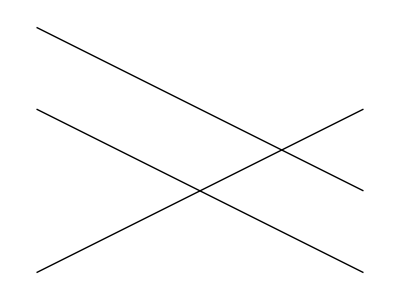

```mathematica
Narisi[d, d2, d3]
```

EnacbaNosilke[Daljica[AA_, BB_]], ki rne enačbo premice nosilke daljice. Primer, za daljico d kot zgoraj je enačba nosilke y == -x/2 + 1/2

```mathematica
ClearAll[x, y]
EnacbaNosilke[Daljica[AA_,BB_]] := Module[{x1, y1, x2, y2, k, n},
{x1, y1}=AA;
{x2, y2}=BB;
k = (y2 - y1)/(x2 - x1);
n =n /.First[Solve[y1 == k*x1 + n, n]];
y ==  k*x + n
]
```

```mathematica
EnacbaNosilke[d]
```

y==1/2-x/2

## Naloga 2

Sestavi funkcijo Presek[Daljica[AA_, BB_], Daljica[CC_, DD_]], ki vrne presečišče daljic, če
se sekata, oziroma prazen seznam ({}).

```mathematica
Presek[Daljica[AA_,BB_],Daljica[CC_,DD_]]:= Module[{resitev},
resitev = Solve[{AA + r(BB - AA) == CC + s(DD - CC), r ≥ 0, r ≤ 1, s ≥ 0, s ≤ 1}, {r, s}];
If[resitev == {},
{},
First[AA + r(BB - AA) /. resitev]
]
]
```

```mathematica
Presek[d, d2]
```

{1,0}

```mathematica
Presek[d, d3]
```

{}

## Naloga 3

Sklenjen mnogokotnik podamo v obliki seznama z glavo Mnogokotnik. Primer
m1 = Mnogokotnik[{0, 0}, {1, 1}, {0, 3}, {-1, 2}]
Ker gre za sklenjen mnogokotnik, predvidevamo, da ima ta povezave med zaporednimi točkami ter od zadnje do prve točke. Sestavi naslednje funkcije :

```mathematica
m1=Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]
m2 =Append[m1,m1[[1]]]
```

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2}]

Mnogokotnik[{0,0},{1,1},{0,3},{-1,2},{0,0}]

Slika[Mnogokotnik[t__]], ki predstavi mnogokotnik s pomočjo grafičnega objekta Line. Najprej sestavi nov seznam točk, ki vključuje obstoječe točke mnogokotnika ter še ponovljeno prvo.Pozor : pazi, da ne izbrišeš obstoječe funkcije za sliko daljice!

```mathematica
Slika[Mnogokotnik[t__]] := Line[{t}]
Slika[m2]
```

Line[{{0,0},{1,1},{0,3},{-1,2},{0,0}}]

Narisi[m__Mnogokotnik], ki nariše enega ali več mnogokotnikov.Pazi, pri risanju moraš narediti tudi daljico od zadnje do začetne točke.Premisli, kako iz obstoječega seznama točk sestaviš nov seznam, ki daljši za eno točko, t.j.ponovljeno prvo točko (Namig : funkciji Append ter First na seznamih.)

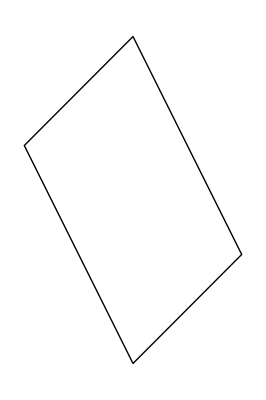

```mathematica
Narisi[m__Mnogokotnik] := Graphics[Slika[m]]
Narisi[m2]
```

PravilniNKotnik[n_, r_], ki nariše pravilni n - kotnik s središčem v točki (0, 0) in s točkami na krožnici z radijem r, pri čemer je ena točka v (r, 0). Namig : uporabi funkcijo Table in upoštevaj, da se točke nahajajo na koordinatah (r cos (2π *i / n, r sin (2π*i / n)) za i = 0, . . . , n − 1. Izriši.

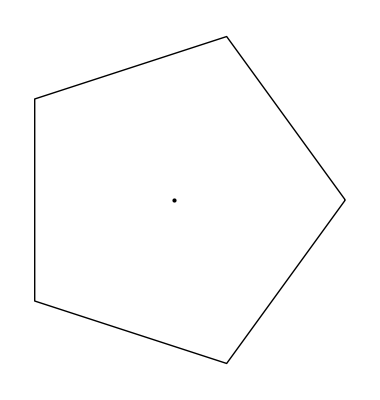

```mathematica
PravilniNKotnik[n_,r_] :=Graphics[{Line[Table[{r*Cos[(2Pi*i)/n],r*Sin[(2Pi*i)/n]},{i,0,n}]],Point[{0,0}]}]
p5 = PravilniNKotnik[5,2]
```

Drugi način (brez uporabe podane formule):

```mathematica
PravilniNKotnik2[n_,r_] := Show[Graphics[{{EdgeForm[Thick],White,RegularPolygon[{0,0},r,n]},{Point[{0,0}]}}]]
p55=PravilniNKotnik2[5,2]
```

-Graphics-

Nadgradi prejšnjo funkcijo v PravilniNKotnik[n_, r_, phi_], ki zgornji pravilni n - kotnik
zavrti za kot phi.Premisli, kako je treba nadgraditi formulo za posamezno točko, da se premakne za kot phi.Rezultat uporabi v kombinaciji s funkcijo Manipulate in interaktivno demonstriraj rotacijo.

```mathematica
PravilniNKotnik[n_,r_,phi_] := Graphics[{Line[Table[{r*Cos[(2Pi*i+phi)/n ],r*Sin[(2Pi*i+phi)/n]},{i,0,n}]],Point[{0,0}]}]
pNeki = Manipulate[PravilniNKotnik[5,2,phi],{phi,1.5,33}]
```

Daljice[Mnogokotnik[t__]], ki vrne seznam daljic, ki tvorijo mnogokotnik.Uporabi funkcijo Partition. V dokumentaciji preveri, kako deluje funkcija ter kako se uporablja zamikanje. Oglej si, kaj naredita naslednja ukaza : 
	Partition[{1, 2, 3, 4, 5}, 2]
	Partition[{1, 2, 3, 4, 5}, 2, 1]

```mathematica
Daljice[Mnogokotnik[t__]] := Map[Daljica,Partition[{t}, 2,1]]
daljice = Daljice[m2]
```

{Daljica[{{0,0},{1,1}}],Daljica[{{1,1},{0,3}}],Daljica[{{0,3},{-1,2}}],Daljica[{{-1,2},{0,0}}]}

```mathematica
Partition[{1,2,3,4,5},2]
Partition[{1,2,3,4,5},2,1]
```

{{1,2},{3,4}}

{{1,2},{2,3},{3,4},{4,5}}

## Naloga 4

Sestavi funkcijo Presek[m_Mnogokotnik, d_Daljica], ki izračuna presečišča mnogokotnika in daljice. Pri tem uporabi že napisane funkcije ter pazi, da rezultat ne istih presečišč večkrat. Poskusi uporabiti vgrajeni funkciji Select in DeleteDuplicates.

```mathematica
Presek2[m_Mnogokotnik,d_Daljica] := Presek[daljice[[1]],d]
Presek2[m2,d]
daljice[[1]]
```

Presek[Daljica[{{0,0},{1,1}}],Daljica[{-1,1},{3,-1}]]

Daljica[{{0,0},{1,1}}]

```mathematica
Presek[d,Slika[d2]]
```

Presek[Daljica[{-1,1},{3,-1}],Line[{{-1,-1},{3,1}}]]

## Naloga 5

Nedokončana

```mathematica
VsiPari[f_,sez1_,sez2_]:=Flatten[Outer[f,sez1,sez2],1]
VsiPari[f,{1,2,3},{a,b}]
```

{f[1,a],f[1,b],f[2,a],f[2,b],f[3,a],f[3,b]}

```mathematica
x = List[{0, 1,5}, {4,5, 6}, {7,9, 3}]
poskus1 = Flatten[x]
poskus3 = Outer[f,x,x]
```

{{0,1,5},{4,5,6},{7,9,3}}

{0,1,5,4,5,6,7,9,3}

{{{{f[0,0],f[0,1],f[0,5]},{f[0,4],f[0,5],f[0,6]},{f[0,7],f[0,9],f[0,3]}},{{f[1,0],f[1,1],f[1,5]},{f[1,4],f[1,5],f[1,6]},{f[1,7],f[1,9],f[1,3]}},{{f[5,0],f[5,1],f[5,5]},{f[5,4],f[5,5],f[5,6]},{f[5,7],f[5,9],f[5,3]}}},{{{f[4,0],f[4,1],f[4,5]},{f[4,4],f[4,5],f[4,6]},{f[4,7],f[4,9],f[4,3]}},{{f[5,0],f[5,1],f[5,5]},{f[5,4],f[5,5],f[5,6]},{f[5,7],f[5,9],f[5,3]}},{{f[6,0],f[6,1],f[6,5]},{f[6,4],f[6,5],f[6,6]},{f[6,7],f[6,9],f[6,3]}}},{{{f[7,0],f[7,1],f[7,5]},{f[7,4],f[7,5],f[7,6]},{f[7,7],f[7,9],f[7,3]}},{{f[9,0],f[9,1],f[9,5]},{f[9,4],f[9,5],f[9,6]},{f[9,7],f[9,9],f[9,3]}},{{f[3,0],f[3,1],f[3,5]},{f[3,4],f[3,5],f[3,6]},{f[3,7],f[3,9],f[3,3]}}}}

## naloga 6

Trikotnik s točkami A (1,2), B (-1,5) in C (4,3) izračunaj entoske vektorje AB, BC in CA, ter nariši trikotnik.

```mathematica
AA = {1,2};
BB ={-1,5};
CC ={4,3};
Vektor[A_,B_]:=Norm[A-B]
```

Definiramo točke trikotnika in nato napišemo funkcijo ki izračuna dolžino vektorja (Razdalja med točkama je enaka dolžini razlike krajevnih vektorjev obeh točk).

```mathematica
EnotskiVektor[A_,B_]:=(B-A)/Vektor[A,B]
```

Funkcija za izračun enotskega vektorja. e = a/(|a|)

```mathematica
EnotskiVektor[AA,BB]
EnotskiVektor[BB,CC]
EnotskiVektor[CC,AA]
```

{-2/(√13),3/(√13)}

{5/(√29),-2/(√29)}

{-3/(√10),-1/(√10)}

```mathematica
trikotnik = {AA,BB,CC}
tocke = Append[trikotnik,trikotnik[[1]]]
```

{{1,2},{-1,5},{4,3}}

{{1,2},{-1,5},{4,3},{1,2}}

Točke damo v skupen seznam. Nakoncu dodamo še prvo točke da bomo lahko lik izrisali.

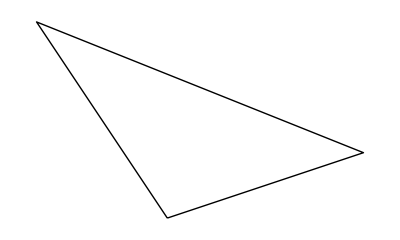

```mathematica
NarisiTrikotnik[tocke_] := Graphics[Line[tocke]]
NarisiTrikotnik[tocke]
```

Funkcija vzame seznam točk, jih spremeni v daljice in narise.